```mathematica
numFullWords[k_Integer, n_Integer] := Sum[(-1)^i Binomial[n, i] (n - i)^k, {i, 0, n-1}]
```

```mathematica
pennProbability[k_Integer, n_Integer] := numFullWords[k - 1, n -1]/n^(k-1)
```

```mathematica
pennCardsProbability[k_Integer] := If[k < 52, 0, pennProbability[k, 52]]
```

```mathematica
probs = Table[N[pennCardsProbability[k]], {k, 0, 1000}];
```

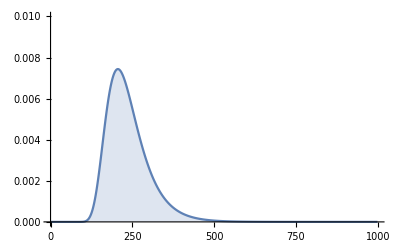

```mathematica
DiscretePlot[ probs[[i]], {i, 1, 999}, PlotRange->{0, 0.01}]
```

```mathematica
𝒟=EmpiricalDistribution[probs -> Range[0, 1000]];
```

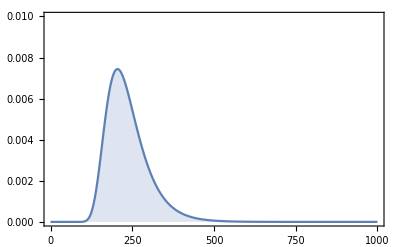

```mathematica
DiscretePlot[PDF[𝒟][x],{x,0,1000},Frame->True,PlotRange->{0,0.01}]
```

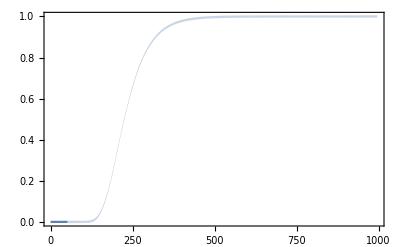

```mathematica
Plot[CDF[𝒟][x],{x,0,1000},Frame->True,PlotRange->{0,1}]
```